```mathematica
f[t_] := (500*1.47)/(20(1.47-.52))(E^(-.52t)-E^(-1.47t));
memLoss[t_] := 14;
anxAndPara[t_] := 9;
```

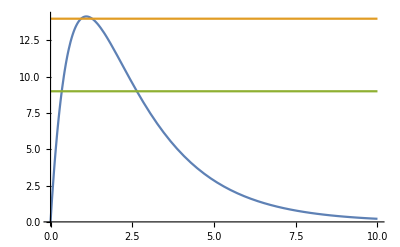

```mathematica
Plot[{f[t], memLoss[t],anxAndPara[t]}, {t,0,10}]
```

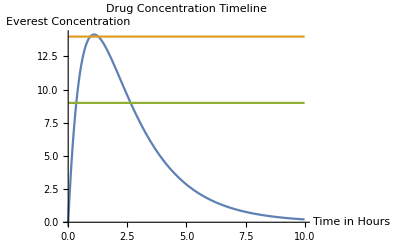

```mathematica
Show[Plot[{f[t], memLoss[t],anxAndPara[t]}, {t,0,10}],AxesLabel->{HoldForm[Time in Hours],HoldForm[Everest Concentration]},PlotLabel->HoldForm[Drug Concentration Timeline],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[Show[Plot[{f[t], memLoss[t],anxAndPara[t]}, {t,0,10}],AxesLabel->{HoldForm[Time in Hours],HoldForm[Everest Concentration]},PlotLabel->HoldForm[Drug Concentration Timeline],LabelStyle->{GrayLevel[0]}],AxesLabel->{Time in Hours,Everest Concentration},PlotLabel->Drug Concentration Timeline,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

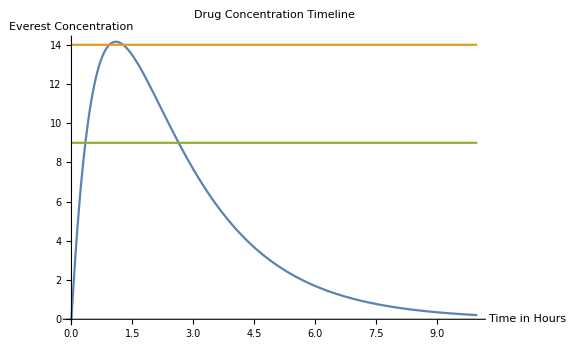

```mathematica
Show[Show[Show[Plot[{f[t], memLoss[t],anxAndPara[t]}, {t,0,10}],AxesLabel->{HoldForm[Time in Hours],HoldForm[Everest Concentration]},PlotLabel->HoldForm[Drug Concentration Timeline],LabelStyle->{GrayLevel[0]}],AxesLabel->{Time in Hours,Everest Concentration},PlotLabel->Drug Concentration Timeline,LabelStyle->{GrayLevel[0]}],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\Austin\\Desktop\\Concentration Graph.png",%13,"PNG"]
```

C:\Users\Austin\Desktop\Concentration Graph.png